## Unit Square N_s=162 μ_a=log(3)=1.09861 μ_s=2log(2)=1.38629 g=0.5

The specific intensity for a triangle centered at (0.63,0.71)
	RULE1		# of point	degree of exactness
	1		7		5
	2		25		10
	4		84		20
	5		126		25

### Bird’s View

RULE1=1

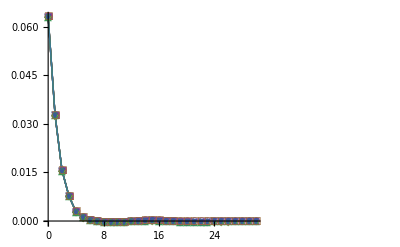

RULE1=1

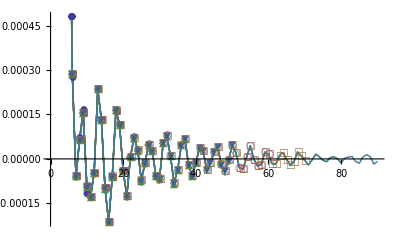

RULE1=2

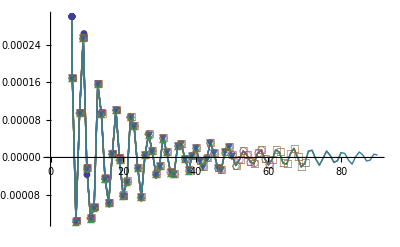

RULE1=4

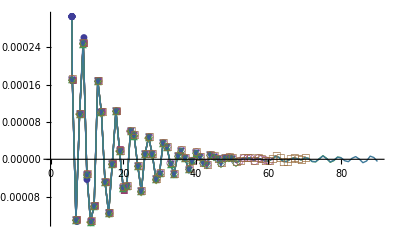

RULE1=5

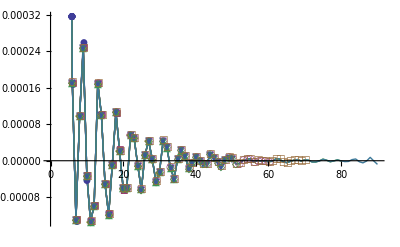

### Zoom In

#### Testing RULE1=1

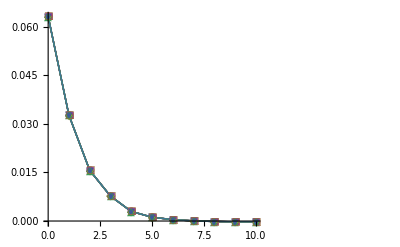

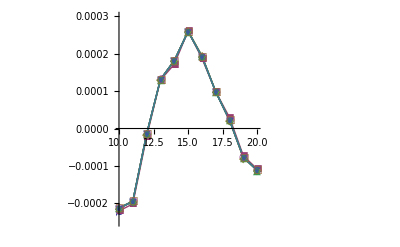

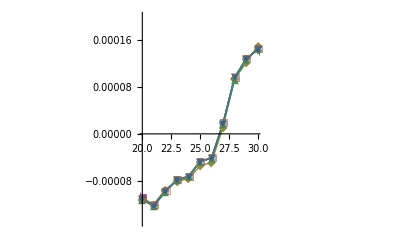

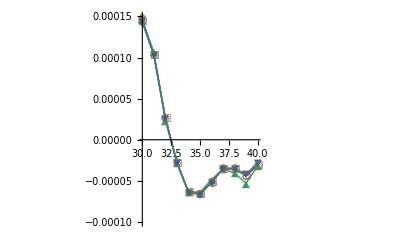

#### Testing RULE1=2

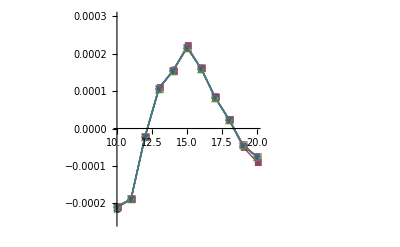

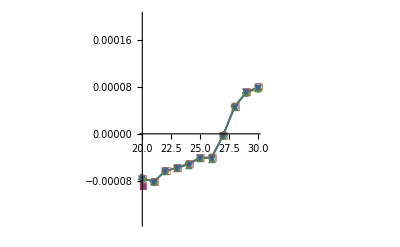

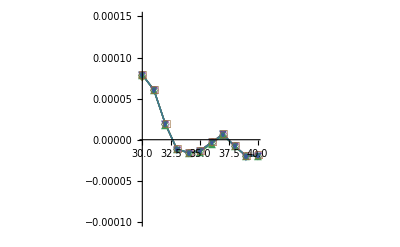

#### Testing RULE1=5

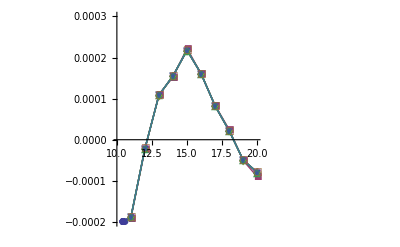

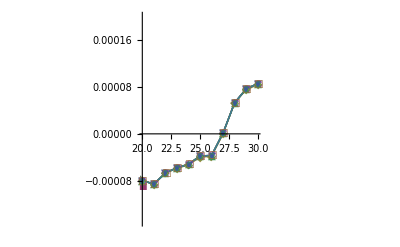

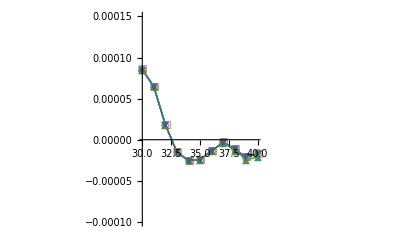

## Approximate Evelope

### centered at (0.63,0.71)

RULE1=1

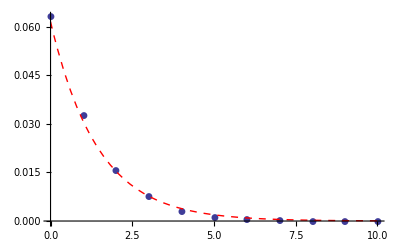

RULE1=2

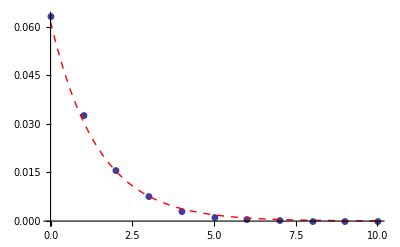

RULE1=5

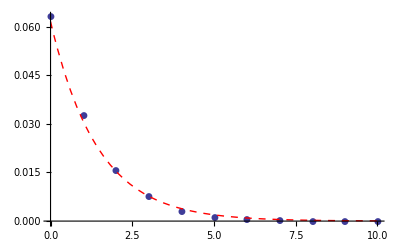

### centered at (0.15,0.76)

RULE1=5

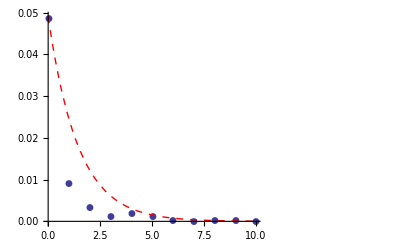

### centered at (0.38, 0.49)

RULE1=5

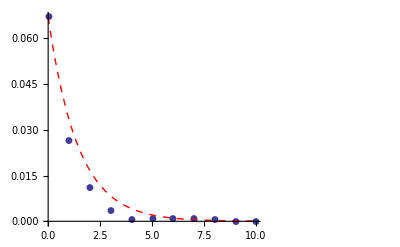

## Unit Square N_s=162 μ_a=log(2)=0.693147 μ_s=5log(2)=3.46574 g=0.9

The specific intensity for a triangle centered at (0.63,0.71)

### Bird’s View

RULE1=1

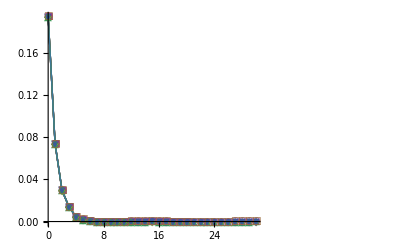

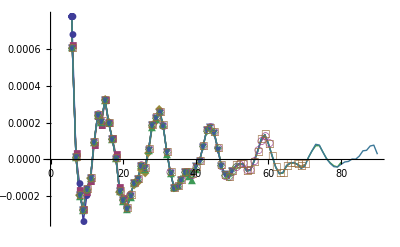

RULE1=2

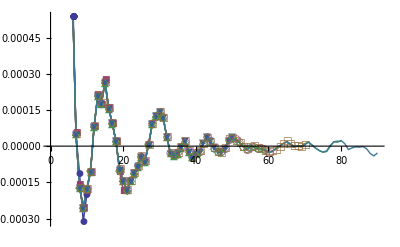

RULE1=1

### Zoom In

#### Testing RULE1=1

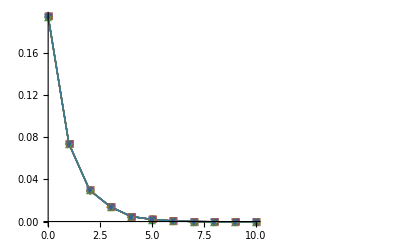

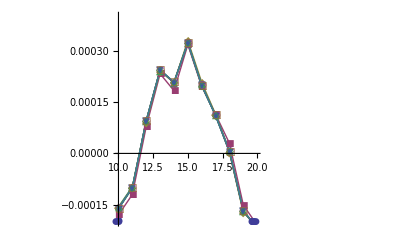

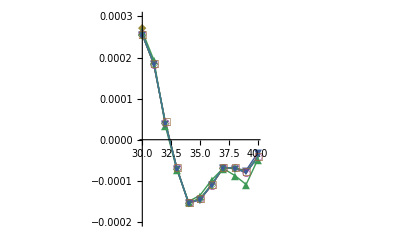

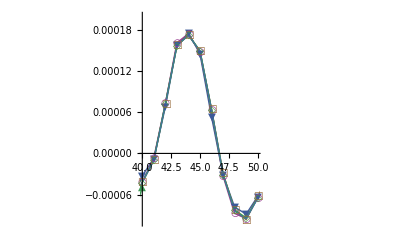

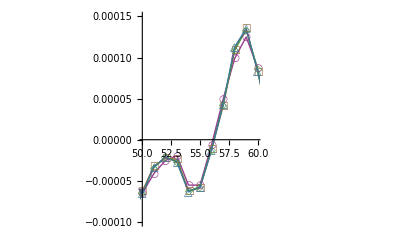

#### Testing RULE1=2

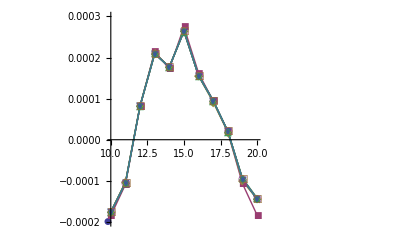

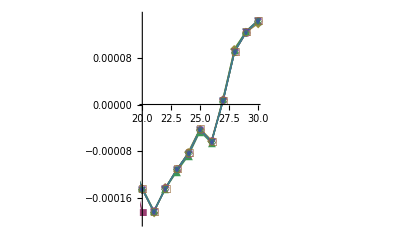

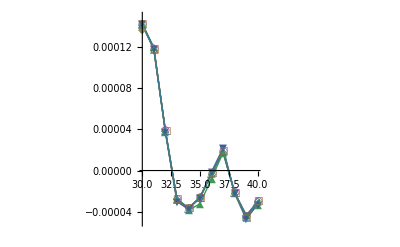

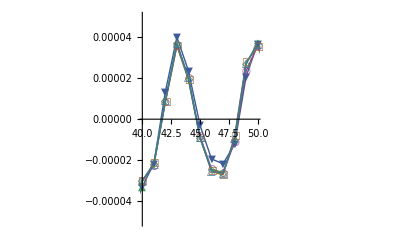

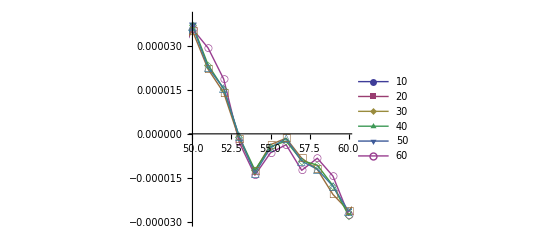

## Plotting Codes

```mathematica
ClearAll[ndlist,raw1,data,RULE1]
RULE1=1;
ndlist=Range[10,90,10];
SetDirectory[NotebookDirectory[]];
raw1=Table[Partition[Import["sol"<>ToString[RULE1]<>"/162_"<>ToString[nd],"Complex128"],2 nd+1],{nd,ndlist}];
ResetDirectory[];
ClearAll[n]
n=20;
Print["RULE1=",RULE1];
(data=Table[Table[{m,raw1[[i,n,m+ndlist[[i]]+1]]},{m,0,ndlist[[i]]}],{i,Length[ndlist]}]//Re)//ListLinePlot[#,PlotRange->Automatic,PlotMarkers->Automatic,PlotLegends->ndlist]&
raw1[[9,n]]//Re//ListPlot[#,PlotRange->Automatic]&;
Show[i=9;Table[{m,raw1[[i,n,m+ndlist[[i]]+1]]},{m,0,ndlist[[i]]}]//Re//ListPlot[#,PlotRange->{{0,10},All},PlotMarkers->Automatic]&,Plot[0.067 0.5^( m),{m,0,90},PlotRange->All,PlotStyle->{Dashed,Thick,Red}]];
```